```mathematica
(* standard *)
x1={0,0};
x2={0.392968737229383,-0.107031262770618};
x3={1.06117158590160,-0.275234111442831};
x4={1.16820284867222,-0.668202848672214};
x5={1,0};
x6={0.892968737229383,0.392968737229382};
x7={1.56117158590160,0.224765888557167};
x8={1.16820284867222,0.331797151327786};
x9={0.500000000000001,0.499999999999999};
x10={0.392968737229383,0.892968737229382};
x11={0.561171585901598,0.224765888557167};
x12={0.668202848672214,-0.168202848672215};

y1={0,0,0};
y2={0.300248668769103,0.275248668769101,-8.12825443129902*^-18};
y3={0.798415043086602,0.752082294451602,-3.03572498862414*^-17};
y4={0.523166374317500,0.451833625682499,1.45198751563439*^-16};
y5={1,0.950000000000000,0};
y6={1.27524866876910,1.25024866876910,9.34269244337375*^-17};
y7={1.77341504308660,1.72708229445160,8.96638245519937*^-17};
y8={1.47316637431750,1.45183362568250,1.45198751563439*^-16};
y9={0.975000000000001,0.974999999999999,1.17929885334723*^-16};
y10={1.25024866876910,1.27524866876910,-8.12825443129904*^-18};
y11={0.773415043086603,0.777082294451601,8.96638245519937*^-17};
y12={0.498166374317501,0.476833625682500,-2.75292531429668*^-18};


t1 = y5 - y1;
t2 = y10 - y2;
t1x = x5 - x1;
t2x = x10 - x2;
```

```mathematica
g1[{x01_,x02_,x03_}] = {x01,x02,x03} + t1;
```

```mathematica
g2[{x01_,x02_,x03_}] ={x01,x02,x03} + t2;
g1x[{x01_,x02_}] = {x01,x02} + t1x;
g2x[{x01_,x02_}] = {x01,x02} + t2x;
```

```mathematica
g1[y1]-y5
```

{0,0.,0}

```mathematica
g2[y2]-y10
```

{0.,0.,0.}

```mathematica
{0.,0.,0.}
g1x[x1] - x5
```

{0.,0.,0.}

{0,0}

```mathematica
g2x[x2] - x10
```

{0.,0.}

```mathematica
IStep = 3; JStep = 3;
```

```mathematica
dPoly = Array[dP,{IStep,JStep}];
```

```mathematica
For[j=1,j<JStep+1,j++,For[i=1,i<IStep+1,i++,dP[i,j]={faceColor,Polygon[{Nest[g1,Nest[g2,y1,j],i],Nest[g1,Nest[g2,y2,j],i],Nest[g1,Nest[g2,y3,j],i],Nest[g1,Nest[g2,y12,j],i]}],faceColor,Polygon[{Nest[g1,Nest[g2,y3,j],i],Nest[g1,Nest[g2,y4,j],i],Nest[g1,Nest[g2,y5,j],i],Nest[g1,Nest[g2,y6,j],i]}],faceColor,Polygon[{Nest[g1,Nest[g2,y6,j],i],Nest[g1,Nest[g2,y7,j],i],Nest[g1,Nest[g2,y8,j],i],Nest[g1,Nest[g2,y9,j],i]}],faceColor,Polygon[{Nest[g1,Nest[g2,y9,j],i],Nest[g1,Nest[g2,y10,j],i],Nest[g1,Nest[g2,y11,j],i],Nest[g1,Nest[g2,y12,j],i]}]};]];
faceColor=RGBColor[0.5,0.1,0.15];
Graphics3D[{EdgeForm[Opacity[.1]],Flatten[dPoly]},Boxed->False,ViewPoint->{0,0,40},ViewVertical->{0,1,0}]
```

-Graphics3D-

```mathematica
(*Graphics3D[{EdgeForm[Opacity[.1]],dPoly},Boxed->False , ViewPoint->{0,0,40}, ViewVertical->{0,1,0}]*)
```

```mathematica
dPolyx = Array[dPx,{IStep,JStep}];
For[j=1,j<JStep+1,j++ ,For[i = 1,i< IStep+1,i++,dPx[i,j]={Polygon[{Nest[g1x,Nest[g2x,x1,j],i],Nest[g1x,Nest[g2x,x2,j],i],Nest[g1x,Nest[g2x,x3,j],i], Nest[g1x,Nest[g2x,x12,j],i]}],Polygon[{Nest[g1x,Nest[g2x,x3,j],i],Nest[g1x,Nest[g2x,x4,j],i],Nest[g1x,Nest[g2x,x5,j],i], Nest[g1x,Nest[g2x,x6,j],i]}], Polygon[{Nest[g1x,Nest[g2x,x6,j],i],Nest[g1x,Nest[g2x,x7,j],i],Nest[g1x,Nest[g2x,x8,j],i], Nest[g1x,Nest[g2x,x9,j],i]}], Polygon[{Nest[g1x,Nest[g2x,x9,j],i],Nest[g1x,Nest[g2x,x10,j],i],Nest[g1x,Nest[g2x,x11,j],i], Nest[g1x,Nest[g2x,x12,j],i]}]}]]
```

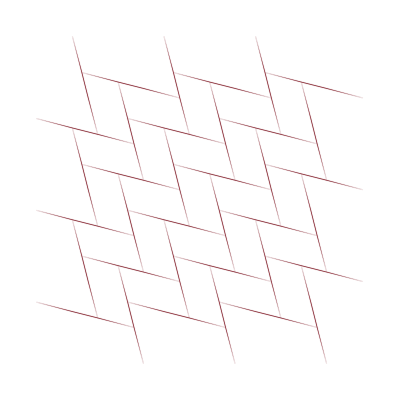

```mathematica
faceTop=RGBColor[1.0,0.8,0.75];  (*lightest,top face*)
faceLeft=RGBColor[0.9,0.6,0.55];  (*medium,left face*)
faceColor=RGBColor[0.5,0.1,0.15];

colors={faceTop,faceLeft};

Graphics[Table[{EdgeForm[Opacity[0.1]],faceColor,dPolyx[[i]]},{i,Length[dPolyx]}],Boxed->False]
```